==================== REGULA FALSI METHOD =========================

f(x) = -1-3 x+2 x^2+x^3

-> Interval : (1,2)

i | p
1 | 1.1
2 | 1.15174
3 | 1.17684
4 | 1.18863
5 | 1.19408
6 | 1.19658
7 | 1.19773
8 | 1.19825
9 | 1.19849
10 | 1.1986

Approximate root = 1.1986

-> Exact roots :- {{x→-2.91223},{x→-0.286462},{x→1.19869}}

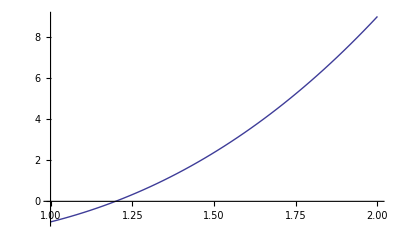

```mathematica
f[x_] := x^3+2 x^2-3x-1;
Print["==================== REGULA FALSI METHOD =========================\n"]
Print["f(x) = ",f[x]];
n=10;
p0 = 1;
p1 = 2;
e = 0.01;
Print["-> Interval : (",p0,",",p1,")"];
output= {};
For[i=0,i<n,i++,
p2 = p1 - f[p1]*(p1-p0)/(f[p1]-f[p0]);

output = AppendTo[output,{i+1,N[p2]}];

If[Abs[p2-p1]<e, Print["Error reduced to ",e, " in ",i+1," iterations ."];
 Break[]];

If[f[p0]*f[p2] < 0,
p1 = p2,
p0 = p2];

];

Print[TableForm[output,
TableHeadings->{None, {"i","p"}}]];
Print["Approximate root = ",N[p2],"\n"];
Print["-> Exact roots :- ",NSolve[f[x]==0,x]]
Plot[f[x],{x,1,2}]
```